Practical-2: Newton Raphson Method
Name: Mehul JhunJhunwala
Roll No: 20221428
B.Sc. (Hons.) Computer Science

Newton Raphson Method: For Given Parameters
Ques-1

x0= 1

Nmax= $Canceled

epsilon= $Canceled

f(x):=Cos[x]

root is: 0.00857564

Estimate error is: 0.991424

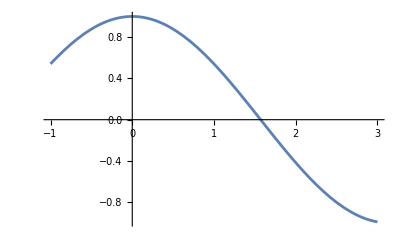

```mathematica
x0 = Input["Enter first guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
g[x_] := Dt[f[x], x];
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x1 = N[x0- (f[x]/.x->x0)/((g[x]/.x->x0))];
	If[Abs[x0-x1] < eps, Return[x1], x0 = x1;];
	Print[i, "th iteration value is: ", x1];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x1];
Print["Estimate error is: ", Abs[x1-x0]];
Plot[f[x], {x, -1, 3}]
```

Ques-2

x0= -2

Nmax= 10

epsilon= 0.001

f(x):=ⅇ^x-Cos[x]

1th iteration value is: -1.28746

estimate error is: 0.

2th iteration value is: -1.29271

estimate error is: 0.

Return[-1.2927]

root is: -1.2927

Estimate error is: 0.0000111035

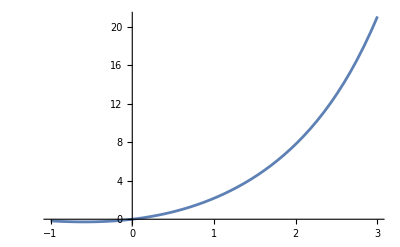

```mathematica
x0 = Input["Enter first guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := ⅇ^x - Cos[x];
g[x_] := Dt[f[x], x];
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x1 = N[x0- (f[x]/.x->x0)/((g[x]/.x->x0))];
	If[Abs[x0-x1] < eps, Return[x1], x0 = x1;];
	Print[i, "th iteration value is: ", x1];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x1];
Print["Estimate error is: ", Abs[x1-x0]];
Plot[f[x], {x, -1, 3}]
```